```mathematica
(**Function for extracting RowBox from documentation**)
Clear[extractFunctionFromRowBox]
extractFunctionFromRowBox[box_]:=ToExpression[Catch @ ReplaceAll[box,f_RowBox:>Throw[f]],StandardForm,Hold]
```

```mathematica
(**Find function example in documentation as RowBox**)
Clear[findFunctionsExampleInDoc]
findFunctionsExampleInDoc[functionName_]:=Flatten[Lookup[WolframLanguageData[functionName,"DocumentationExampleInputs"],"BasicExamples"]]
```

```mathematica
(**Pick a random sample from documentation about functionName**)
Clear[extractRandomFunction]
Clear[extractNFunction]
extractRandomFunction[functionName_]:=extractFunctionFromRowBox[RandomChoice[findFunctionsExampleInDoc[functionName]]]
extractNFunction[functionName_,n_]/; 0<n&&n≤Length[findFunctionsExampleInDoc[functionName]]:=extractFunctionFromRowBox[findFunctionsExampleInDoc[functionName][[n]]]
```

```mathematica
(**Usage example**)
extractRandomFunction["Sin"]
extractRandomFunction["Select"]
```

Hold[Plot[Sin[x],{x,0,2 π}]]

Hold[Select[{1,2,4,7,6,2},EvenQ]]

```mathematica
(**Substitute part of the function with ?**)
Clear[tweakFunction]
(**SetAttributes[tweakFunction,HoldFirst]**)
ClearAttributes[tweakFunction,HoldFirst]
tweakFunction[Hold[expr_]]:=With[
{l=RandomInteger[{0,Length[Unevaluated[expr]]}]},
ReplacePart[HoldForm[expr],{1,l}->Placeholder["?"]]]
(**Better use this one the other is not fair!**)
tweakFunction[Hold[expr_],n_]/; 0≤ n≤ Length[Unevaluated[expr]]:=ReplacePart[HoldForm[expr],{1,n}->Placeholder["?"]]
(**this is very unsafe to use but wonderful**)
tweakFunction[Hold[expr_],n_List]:=With[
{s=n/.List->Sequence},
ReplacePart[HoldForm[expr],{1,s}->Placeholder["?"]]]
```

```mathematica
(**Usage example**)
tweakFunction[extractNFunction["NestGraph",2],2]
```

NestGraph[Mod[#1^2+1,10]&,?,VertexLabels→Name]

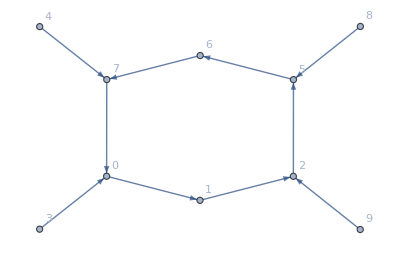

```mathematica
NestGraph[Mod[#1^2+1,10]&,Range[0,9],VertexLabels->"Name"]
```

```mathematica
tweakFunction[extractNFunction["NestGraph",2],{1,1,1}]
```

NestGraph[Mod[?,10]&,Range[0,9],VertexLabels→Name]

```mathematica
Table[extractNFunction["NestGraph",i],{i,1,Length[findFunctionsExampleInDoc["NestGraph"]]}]
```

{Hold[NestGraph[f,x,3,VertexLabels→Name,ImagePadding→40]],Hold[NestGraph[Mod[#1^2+1,10]&,Range[0,9],VertexLabels→Name]],Hold[NestGraph[{f[#1],g[#1]}&,x,3,VertexLabels→Name]],Hold[NestGraph[#1[BorderingCountries]&,Switzerland,2,VertexLabels→Name]]}

```mathematica
(**
Avoid removing some attribute
**)

Clear[findRemovableAttribute]
(**findRemovableAttribute[Hold[attr_Integer]]:=True
findRemovableAttribute[Hold[attr_Real]]:=True
findRemovableAttribute[Hold[attr_Symbol]]:=True
findRemovableAttribute[Hold[g__Graphics]]:=False
findRemovableAttribute[Hold[g__Image]]:=False
findRemovableAttribute[Hold[Sequence[attr__]]]/;
Length[Unevaluated[attr]]>1&&
Unevaluated[attr][[0]]==Sequence:=Map[findRemovableAttribute,List@Map[Hold,Unevaluated[attr]]]
findRemovableAttribute[Hold[Sequence[attr__]]]:=Hold[attr](**Never call this**)
findRemovableAttribute[Hold[expr_[attr___]]]/;attr=={}:=True
findRemovableAttribute[Hold[expr_[attr__]]]:={True,Map[findRemovableAttribute,List@Map[Hold,Unevaluated[attr]]]}
findRemovableAttribute[Hold[expr_[attr_]]]:={True,findRemovableAttribute[Hold[attr]]}
findRemovableAttribute[Hold[attr__]]:=False String and unexpected stuff**)
```

```mathematica
extractNFunction["ImageCompose",2]
```

Hold[ImageCompose[-Graphics-,-Graphics-,Scaled[{0.5,0.9}]]]

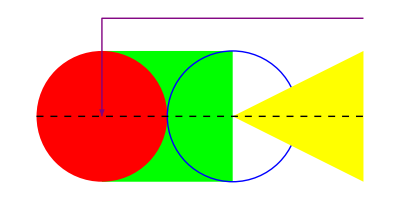
Hold[-Graphics-]

```mathematica
extractNFunction["Graphics",1]
```

```mathematica
SetAttributes[SymbolQ,HoldFirst]
SymbolQ[Image|Graph|Graphics|Graphics3D]:=False
SymbolQ[_]:=True
example=Hold[Map[f,{1,2,3}]];
pattern=_Symbol?SymbolQ;
With[
{pos=Position[example,pattern]},
Map[Extract[example,#,Function[i,#:>i,HoldFirst]]&,pos]
]
```

{{0}:>Hold,{1,0}:>Map,{1,1}:>f,{1,2,0}:>List}

```mathematica
Clear[removeExpressionPart]
SetAttributes[removeExpressionPart,HoldAllComplete]
(**pattern=_Symbol?SymbolQ**)
pattern=_Image|_Graph|_Graphics|_Graphics3D;
removeExpressionPart[expr_,pattern_]:=expr/.pattern->Placeholder[]
```

```mathematica
removeExpressionPart[Hold[-Graphics-],pattern]
```

Hold[□]

```mathematica
positionsOfRemovablePart[removeExpressionPart[Hold[ImageCompose[-Graphics-,-Graphics-,Scaled[{0.5,0.9}]]],pattern]]
```

{{0}:>ImageCompose,{3,0}:>Scaled,{3,1,1}:>0.5,{3,1,2}:>0.9,{3,1}:>□[0.5,0.9],{3}:>Scaled[□[0.5,0.9]],{0}:>ImageCompose[□,□,Scaled[□[0.5,0.9]]]}

```mathematica
ReplaceAll[Hold[ImageCompose[□,□,Scaled[{0.5,0.9}]]]]
```

ReplaceAll[Hold[ImageCompose[□,□,Scaled[{0.5,0.9}]]]]

```mathematica
Clear[positionsOfRemovablePart]
SetAttributes[positionsOfRemovablePart,HoldAllComplete]
positionsOfRemovablePart[exrp_]:=With[
{pos=Position[exrp,Except[Placeholder|_Placeholder|Hold|Rule|RuleDelayed|List|_List]]},
Map[Extract[exrp,#,Function[i,If[Length[Rest[#]]==0,{0},Rest[#]]:>i,HoldFirst]]&,pos][[1;;-2]]
]
```

```mathematica
Placeholder[]//FullForm
```

Placeholder[]

```mathematica
positionsOfRemovablePart[Hold[List[1,2,3]]]
```

{{1}:>1,{2}:>2,{3}:>3}

```mathematica
□[0.5,0.9]//FullForm
```

\[Placeholder][0.5,0.9]

```mathematica
Head[Placeholder[]]
```

Placeholder

```mathematica
Clear[listRemovablePartFromEspression]
SetAttributes[listRemovablePartFromEspression,HoldAllComplete]
listRemovablePartFromEspression[espr_,pattern_]:=positionsOfRemovablePart[removeExpressionPart[espr,pattern]]
```

```mathematica
(**Example**)
Clear[g]
Clear[l]
Clear[p]
g=extractRandomFunction["ImageCompose"]
l=listRemovablePartFromEspression[g,pattern]
p=First[l[[RandomInteger[{1,Length[l]}]]]]
tweakFunction[g,p]
ReleaseHold[g]
```

Hold[ImageCompose[-Graphics-,-Graphics-,{Center,Top},{Center,Top}]]

{{0}:>ImageCompose,{3,1}:>Center,{3,2}:>Top,{4,1}:>Center,{4,2}:>Top,{0}:>ImageCompose[□,□,{Center,Top},{Center,Top}]}

{4,2}

ImageCompose[-Graphics-,-Graphics-,{Center,Top},{Center,?}]

-Graphics-

0

?[-Graphics-,-Graphics-,Scaled[{0.5,0.9}]]

```mathematica
Last[l]
```

{}

```mathematica
{1,3,1,2}[[2;;All]]
```

{3,1,2}

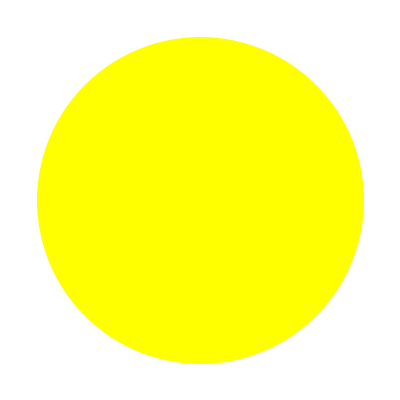
```mathematica
listRemovablePartFromEspression[Hold[ImageCompose[-Graphics-,{-Graphics-,0.5}]],pattern]
```

{{0}:>ImageCompose,{2,2}:>0.5,{0}:>ImageCompose[□,{□,0.5}]}